Getting the chemical class information

```mathematica
cc=ChemicalData["Classes"];
```

Getting the information of amino acid

```mathematica
AA=ChemicalData["AminoAcids"]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
num = Length[AA]
```

20

```mathematica
AAName=Map[ChemicalData[#,"Name"]&,AA]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
AAFig=Map[ChemicalData[#]&,AA];
```

```mathematica
AAFig45=Map[Graphics[#[[1]] , ImageSize->45]&, AAFig]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(AAAdjMat=Map[(ChemicalData[#,"AdjacencyMatrix"]//Normal)&,AA])//Short
```

{{{0,1,1,0,0,0,0,0,1,1},{1,0,0,1,2,0,0,0,0,0},«6»,{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},«18»,{«1»}}

```mathematica
AAVT=Map[ChemicalData[#,"VertexTypes"]&,AA]
```

{{C,C,N,O,O,H,H,H,H,H},{O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,N,O,O,H,H,H,H,C,O,C,H,H,H,H,H},{S,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,O,O,H,H,H,H,H,H,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{S,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,C,N,N,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,O,C,C,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,N,C,C,C,H,C,H,H,H,H,H,H,H,N,C,H,H,H,O,O,H}}

```mathematica
(elmAAAdjMat=Table[elementAdjMat[AAAdjMat[[n]],AAVT[[n]]],{n,Length[AAAdjMat]}])//Length
```

20

```mathematica
(AADmat=Outer[eigenSpectrumDistance,elmAAAdjMat,elmAAAdjMat,1])//Dimensions
```

{20,20}

Getting the information of lipids

```mathematica
LP=ChemicalData["Lipids"]
```

{heptane-1-13 C,heptane-d 16,octanoic acid-1-13 C,octanoic acid-1,2,3,4-13 C4,2-keto-4-methylpentanoic acid-1-13 csodium salt,octanoic-d 15 acid,sodium octanoate-1-13 C,menadione,decanoic acid-1-13 C,decanoic-d 19 acid,lauric acid-12-13 C,lauric acid-1-13 C,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-1-13 C,myristic acid-1,2-13 C2,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-1-13 C,palmitic acid-2-13 C,palmitic acid-1,2-13 C2,palmitic acid-2,2-d 2,palmitic acid-13 C16,oleic acid-1-13 C,stearic acid-1-13 C,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-1-13 C,potassium palmitate-2,2-d 2,oleic acid-13 C18,stearic-d 35 acid,octanoic acid-7-13 C,dodecylphosphorylcholine-d 38,α-tocopherol,glyceryl tri(octanoate-1-13 C),glyceryl-2-13 ctripalmitate,glyceryl tri(palmitate-1-13 C),glyceryl tri(oleate-1-13 C)}

```mathematica
lipidsName=Map[ChemicalData[#,"Name"]&,LP]
```

{heptane-1-13 C,heptane-d 16,octanoic acid-1-13 C,octanoic acid-1,2,3,4-13 C4,2-keto-4-methylpentanoic acid-1-13 csodium salt,octanoic-d 15 acid,sodium octanoate-1-13 C,menadione,decanoic acid-1-13 C,decanoic-d 19 acid,lauric acid-12-13 C,lauric acid-1-13 C,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-1-13 C,myristic acid-1,2-13 C2,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-1-13 C,palmitic acid-2-13 C,palmitic acid-1,2-13 C2,palmitic acid-2,2-d 2,palmitic acid-13 C16,oleic acid-1-13 C,stearic acid-1-13 C,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-1-13 C,potassium palmitate-2,2-d 2,oleic acid-13 C18,stearic-d 35 acid,octanoic acid-7-13 C,dodecylphosphorylcholine-d 38,α-tocopherol,glyceryl tri(octanoate-1-13 C),glyceryl-2-13 ctripalmitate,glyceryl tri(palmitate-1-13 C),glyceryl tri(oleate-1-13 C)}

```mathematica
isoQ=Table[StringMatchQ[lipidsName[[n]],RegularExpression[".*13 {0,1}[Cc].*"]],{n,Length[lipidsName]}]
```

{True,False,True,True,True,False,True,False,True,False,True,True,False,False,False,True,True,False,False,False,True,True,True,False,True,True,True,False,False,False,True,False,True,False,True,False,False,True,True,True,True}

```mathematica
nonIsoPos=Position[isoQ,False]
```

{{2},{6},{8},{10},{13},{14},{15},{18},{19},{20},{24},{28},{29},{30},{32},{34},{36},{37}}

```mathematica
lipidsNonIso=LP[[nonIsoPos//Flatten]]
```

{heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

Merging and Clustering

```mathematica
LPAA=Flatten[{AA,lipidsNonIso}]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan,heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

```mathematica
numLPAA=Length[LPAA]
```

38

```mathematica
LPAAName=Map[ChemicalData[#,"Name"]&,LPAA]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan,heptane-d 16,octanoic-d 15 acid,menadione,decanoic-d 19 acid,lauric-2,2-d 2acid,lauric acid-12,12,12-d 3,lauric-d 23 acid,myristic acid-14,14,14-d 3,DL-3-hydroxytetradecanoic acid-2,2,3,4,4-d 5,myristic-d 27 acid,palmitic acid-2,2-d 2,stearic acid-2,2-d 2,stearic acid-18,18,18-d 3,palmitic-d 31 acid,potassium palmitate-2,2-d 2,stearic-d 35 acid,dodecylphosphorylcholine-d 38,α-tocopherol}

```mathematica
(LPAAFig=Map[ChemicalData[#]&,LPAA])//Length
```

38

```mathematica
LPAAFig45=Map[Graphics[#[[1]] , ImageSize->45]&, LPAAFig]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(LPAAAdjMat=Map[(ChemicalData[#,"AdjacencyMatrix"]//Normal)&,LPAA])//Short
```

{{{0,1,1,0,0,0,0,0,1,1},{1,0,0,1,2,0,0,0,0,0},«7»,{1,0,0,0,0,0,0,0,0,0}},«36»,{«1»}}

```mathematica
LPAAVT=Map[ChemicalData[#,"VertexTypes"]&,LPAA]
```

{{C,C,N,O,O,H,H,H,H,H},{O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,N,O,O,H,H,H,H,C,O,C,H,H,H,H,H},{S,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,O,O,H,H,H,H,H,H,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{S,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,C,N,N,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,O,C,C,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,N,C,C,C,H,C,H,H,H,H,H,H,H,N,C,H,H,H,O,O,H},{C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{K,O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{P,O,O,O,O,N,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H}}

```mathematica
(elmLPAAAdjMat=Table[elementAdjMat[LPAAAdjMat[[n]],LPAAVT[[n]]],{n,Length[LPAAAdjMat]}])//Length
```

38

```mathematica
(LPAADmat=Outer[eigenSpectrumDistance,elmLPAAAdjMat,elmLPAAAdjMat,1])//Dimensions
```

{38,38}

```mathematica
lpaaag["W"]=DirectAgglomerate[LPAADmat,Linkage->"Ward"]
```

DirectAgglomerate::ties: 3 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],Cluster[3,6,0.71254,1,1],1.05103,2,2],1.43447,1,4],Cluster[Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.951732,2,1],1.02298,1,3],Cluster[5,15,0.466146,1,1],1.43198,4,2],Cluster[21,Cluster[22,24,1.00798,1,1],2.20387,1,2],3.62661,6,3],6.28158,5,9],Cluster[Cluster[16,18,0.92273,1,1],Cluster[Cluster[Cluster[10,14,0.468095,1,1],11,0.592902,2,1],12,0.723301,3,1],3.19682,2,4],7.67005,14,6],Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[34,31,0.,1,1],35,0.244229,2,1],Cluster[Cluster[30,28,0.,1,1],29,0.774995,2,1],2.23878,3,3],37,2.3346,6,1],Cluster[33,Cluster[32,36,0.,1,1],0.,1,2],3.68258,7,3],Cluster[27,Cluster[25,26,0.,1,1],0.,1,2],5.51745,10,3],Cluster[Cluster[Cluster[17,19,0.588454,1,1],Cluster[20,23,0.961533,1,1],2.31466,2,2],38,6.97161,4,1],10.7161,13,5],36.6737,20,18]

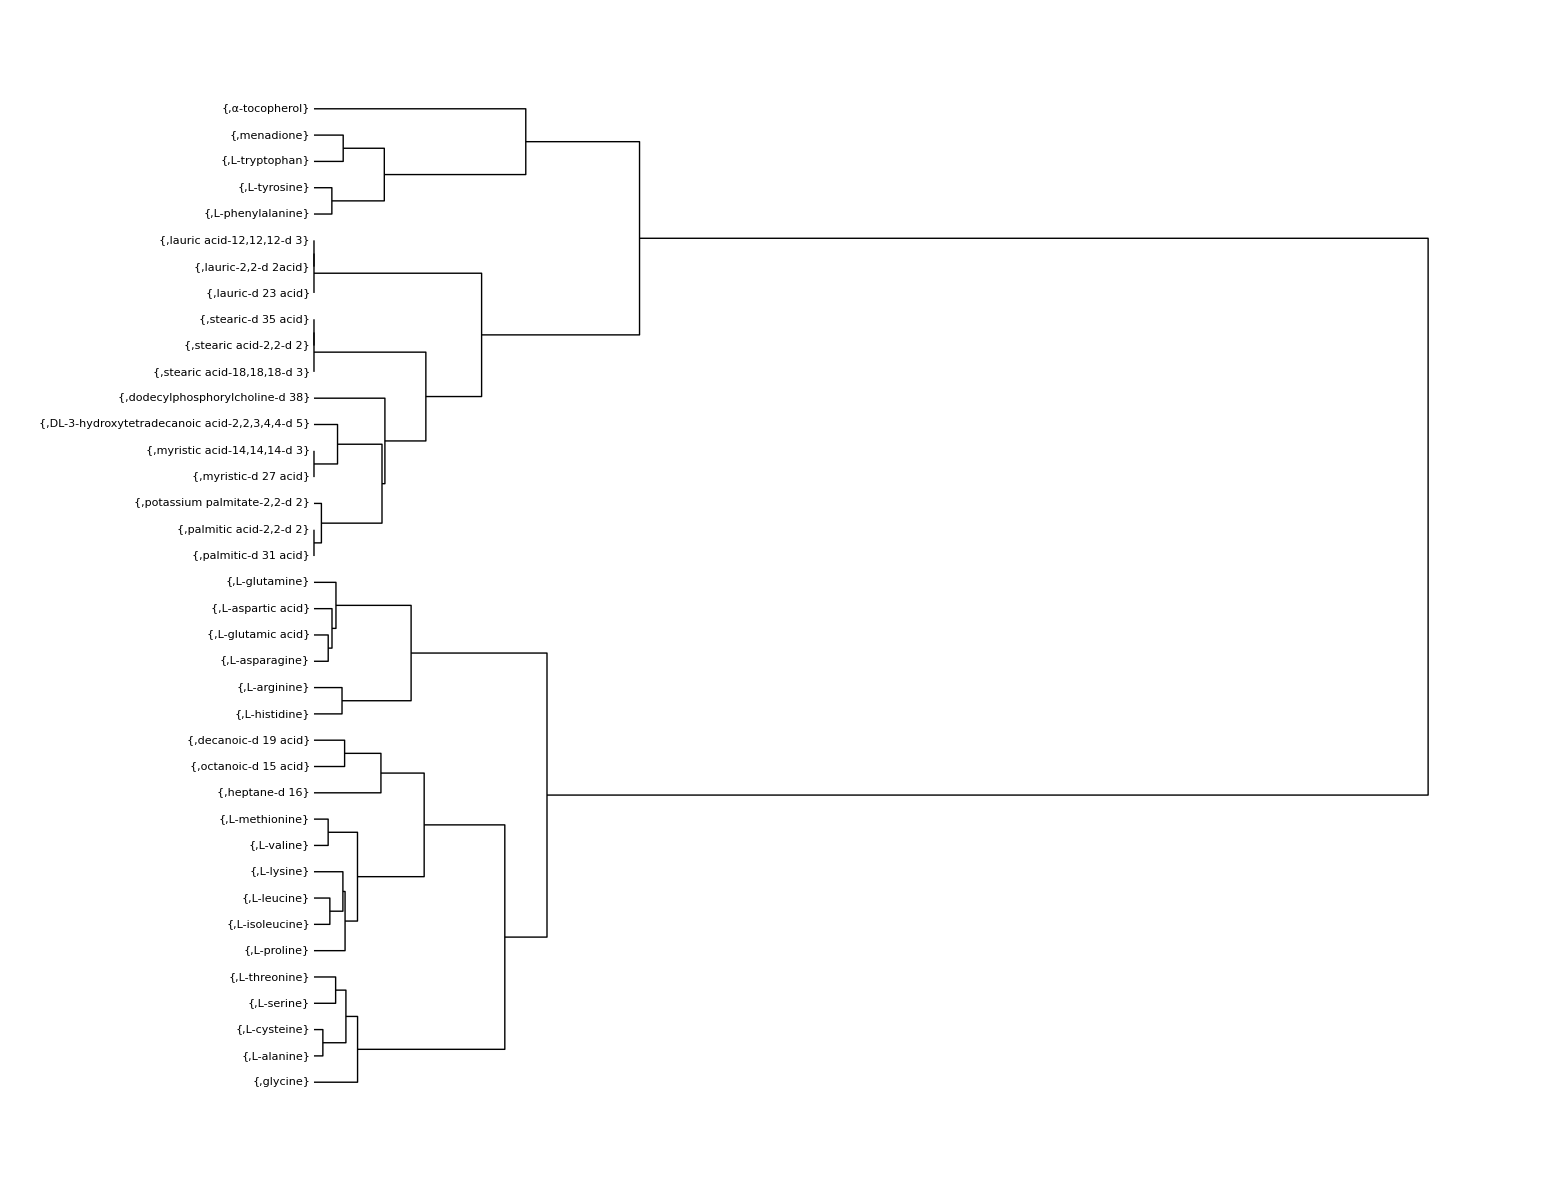

```mathematica
DendrogramPlot[lpaaag["W"],LeafLabels->({LPAAFig45[[#]],LPAAName[[#]]}&),Orientation->Right,AspectRatio->0.76]
```